```mathematica
Rμ = 8.314;
T1= 4400;
p1 = 20.7 10^6;
μg = 20.3 10^-3;
κ = 1.20;(*κ=k*)
mdot = 333;
p3 = 0.05 10^6;
κ = 1.20;
Rg = Rμ/μg
```

409.557

```mathematica
ρ1=p1/(Rg  T1)
```

11.4869

```mathematica
Assuming[{κ>0,p1>0,r1>0},Maximize[√((2  κ p1 ρ1)/(κ -1) z^(2/κ)(1-z^((κ-1)/κ))),z]]
```

{10000.4,{z→0.564474}}

```mathematica
Solve[D[√((2  κ p1 ρ1)/(κ -1) z^(2/κ)(1-z^((κ-1)/κ))),z]==0,z]
```

{{z→0.564474}}

```mathematica
(*D[√((2  κ p1 ρ1)/(κ -1) z^(2/κ)(1-z^((κ-1)/κ))),z]*)
```

```mathematica
(*Solve[(31237.981684170663 (1.6260162601626016 (1-z^0.18699186991869918) z^0.6260162601626016-0.18699186991869918 z^0.8130081300813008))/(√((1-z^0.18699186991869918) z^1.6260162601626016))==0,z]*)
```

```mathematica
zast=(2/(κ+1))^(κ/(κ-1))
```

0.564474

```mathematica
fsqrt[zz_]:=√((2  κ p1 ρ1)/(κ -1) zz^(2/κ)(1-zz^((κ-1)/κ)))
```

```mathematica
sqrtzast=fsqrt[zast]
```

10000.4

```mathematica
Fast=mdot/sqrtzast
```

0.0332986

```mathematica
(*Solve[mdot/sqrtzast==F,F]*)
```

```mathematica
Solve[Fast==(π Dast^2)/4,Dast]
```

{{Dast→-0.205906},{Dast→0.205906}}

```mathematica
Reduce[p1/ρ1^κ==p3/ρ3^κ,ρ3]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ρ3==0.0757478

```mathematica
Solve[p1/ρ1^κ==p3/ρ3^κ,ρ3]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ρ3→0.0757478}}

```mathematica
ρ3n=0.09856524252428155
```

0.0985652

```mathematica
T3=(ρ3n/ρ1)^(κ-1)T1
```

1698.86

```mathematica
ρ=p3/(Rg T3)
```

0.071862

```mathematica
z3=p3/p1
```

0.00241546

```mathematica
sqrt3=fsqrt[z3]
```

280.406

```mathematica
F3=mdot/sqrt3
```

1.18756

```mathematica
Solve[F3==(π D3^2)/4,D3]
```

{{D3→-1.22966},{D3→1.22966}}

```mathematica
w=√((2 κ Rg T1)/(κ-1)(1 - (p3/p1)^((κ-1)/κ)))
```

3701.83

```mathematica
(**)
```

```mathematica
past=zast p1
```

1.16846×10^7

```mathematica
Solve[past/ρast^κ==p1/ρ1^κ,ρast]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ρast→7.13248}}

```mathematica
ρastn=9.130118269778048
```

9.13012

```mathematica
vast=mdot/(ρastn Fast)
```

1095.32

```mathematica
(**)
```

```mathematica
p01=10^5;
```

```mathematica
p02=0;
```

```mathematica
P1=mdot w + (p3-p01)F3
```

1.17333×10^6

```mathematica
P2=mdot w + (p3-p02)F3
```

1.29209×10^6

```mathematica
(**)
```

```mathematica
pF=mdot/Fast -  ((px past)/(T1 Rg)ρ1^(κ-1))^(1/κ)√((2 κ Rg T1)/(κ-1)(1 - ((px past)/p1)^((κ-1)/κ)))  Fx
```

10000.4-33167.6 Fx √(1-0.909091 px^0.166667) px^0.833333

```mathematica
(*pFnew[Fx_,px_]:=mdot/Fast -  (px/(T1 Rg)ρ1^(κ-1))^(1/κ)√((2 κ Rg T1)/(κ-1)(1 - (px/p1)^((κ-1)/κ)))  Fx*)
```

```mathematica
(*pFnew[F3/Fast,p3/past]*)
```

```mathematica
(*ContourPlot[pFnew[Fx]==0,{Fx, 1, F3/Fast}, {px,1,p3/past}]*)
```

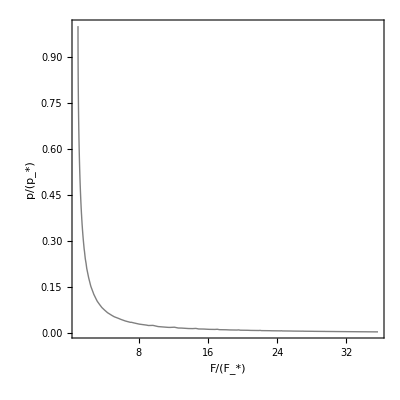

```mathematica
p1=ContourPlot[pF==0,{Fx, 1, F3/Fast}, {px,1,p3/past},AxesStyle->Black,ContourStyle->{Gray,Thick},FrameLabel->{Style["F/(F_*)",16,Black,FontFamily->"Times"], Style[Rotate["p/(p_*)",270 Degree],16,Black,FontFamily->"Times"]}, LabelStyle->{16,Black,FontFamily->"Times New Roman"}, AspectRatio->1(*,GridLines->Automatic,GridLinesStyle->Directive[Dashed,Gray]*)(*,PlotLabel->Style[p/(p_*)[F/(F_*)],16]*)]
```

```mathematica
(**)
```

```mathematica
Tast=(ρastn/ρ1)^(κ-1)T1
```

4202.5

```mathematica
(*Плохой вариант, так не строит!*)
```

```mathematica
(*TF=mdot/Fast -  ((Tx Tast)/T1)^(1/(κ-1))ρ1 √((2 κ Rg T1)/(κ-1)(1 - ((((Tx Tast)/T1)ρ1 Rg Tx Tast)/p1)^((κ-1)/κ)))  Fx*)
```

```mathematica
(*p2=ContourPlot[TF==0,{Fx, 1, F3/Fast}, {Tx,1,T3/Tast},AxesStyle->Black,ContourStyle->{Blue,Thick},FrameLabel->{Style["F/(F_*)",16,Black,FontFamily->"Times"], Style[Rotate["T/(T_*)",270 Degree],16,Black,FontFamily->"Times"]}, LabelStyle->{16,Black,FontFamily->"Times New Roman"}, AspectRatio->1]*)
```

```mathematica
(*Нужно взять другое выражение для скорости v!*)
```

```mathematica
TF=mdot/Fast -  ((Tx Tast)/T1)^(1/(κ-1))ρ1 √((2 κ Rg)/(κ-1)(T1 - Tx Tast))  Fx
```

10000.4-640.065 Fx √(4400-4202.5 Tx) Tx^5.

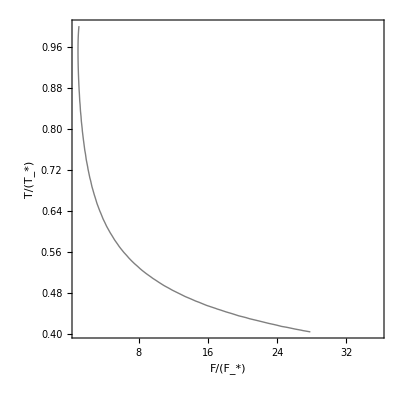

```mathematica
p2=ContourPlot[TF==0,{Fx, 1, F3/Fast}, {Tx,1,T3/Tast},AxesStyle->Black,ContourStyle->{Gray,Thick},FrameLabel->{Style["F/(F_*)",16,Black,FontFamily->"Times"], Style[Rotate["T/(T_*)",270 Degree],16,Black,FontFamily->"Times"]}, LabelStyle->{16,Black,FontFamily->"Times New Roman"}, AspectRatio->1(*,GridLines->Automatic,GridLinesStyle->Directive[Dashed,Gray]*)(*,PlotLabel->Style[p/(p_*)[F/(F_*)],16]*)]
```

```mathematica
(**)
```

```mathematica
ρF=mdot/Fast -  ρx ρastn √((2 κ Rg T1)/(κ-1)(1 - ((ρx ρastn)/ρ1)^(κ-1)))  Fx
```

10000.4-42457.1 Fx √(1-0.955113 ρx^0.2) ρx

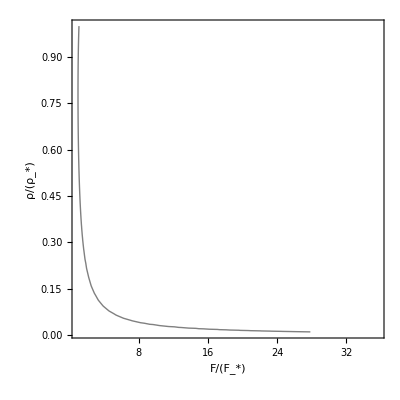

```mathematica
p3=ContourPlot[ρF==0,{Fx, 1, F3/Fast}, {ρx,1,ρ3n/ρastn},AxesStyle->Black,ContourStyle->{Gray,Thick},FrameLabel->{Style["F/(F_*)",16,Black,FontFamily->"Times"], Style[Rotate["ρ/(ρ_*)",270 Degree],16,Black,FontFamily->"Times"]}, LabelStyle->{16,Black,FontFamily->"Times New Roman"}, AspectRatio->1(*,GridLines->Automatic,GridLinesStyle->Directive[Dashed,Gray]*)(*,PlotLabel->Style[p/(p_*)[F/(F_*)],16]*)]
```

```mathematica
(**)
```

```mathematica
vF=mdot/Fast -  (1-((vx vast)^2(κ-1))/(2 κ Rg T1))^(1/(κ-1))ρ1 vx vast Fx
```

10000.4-12581.9 Fx vx (1-0.0554798 vx^2)^5.

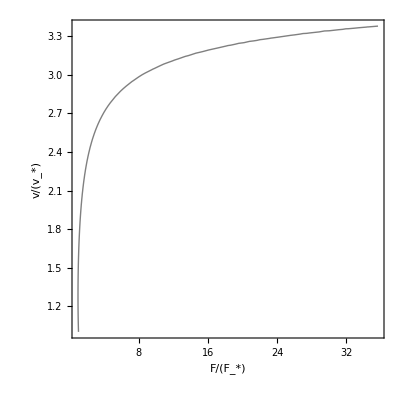

```mathematica
p4=ContourPlot[vF==0,{Fx, 1, F3/Fast}, {vx,1,w/vast},AxesStyle->Black,ContourStyle->{Gray,Thick},FrameLabel->{Style["F/(F_*)",16,Black,FontFamily->"Times"], Style[Rotate["v/(v_*)",270 Degree],16,Black,FontFamily->"Times"]}, LabelStyle->{16,Black,FontFamily->"Times New Roman"}, AspectRatio->1(*,GridLines->Automatic,GridLinesStyle->Directive[Dashed,Gray]*)(*,PlotLabel->Style[p/(p_*)[F/(F_*)],16]*)]
```